```mathematica
SetDirectory[NotebookDirectory[]];
SetOptions[ListPlot,Frame-> True,GridLines-> Automatic,ImageSize-> 600,PlotStyle-> Red,PlotRange-> Full];
```

```mathematica
map=Import["testtopomap.txt","Table"];
```

```mathematica
cl=Table[Table[
If[EuclideanDistance[{-3,3},m[[i*20+j]]]<EuclideanDistance[{3,-3},m[[i*20+j]]],
Blue,
Red],
{j,1,20,1}],
{i,0,19,1}]//TableForm
```

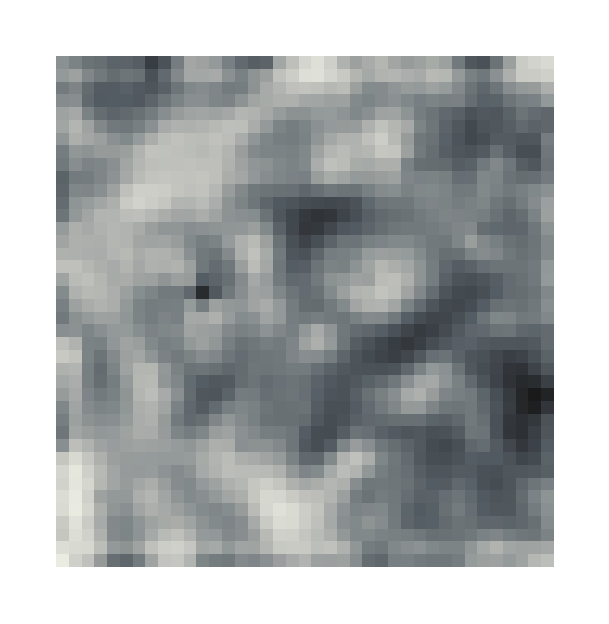

```mathematica
maptrunc=map[[;;,;;39]];
ArrayPlot[maptrunc,ColorFunction-> ColorData[{"GrayTones",{Max[maptrunc],Min[maptrunc]}}],ColorFunctionScaling-> False]
```

#### Test with bivariate norm

```mathematica
d=Import["testdata.txt","CSV"][[;;,2;;3]];
m=Import["testmodel.txt","Table"];
(*h =Partition[Import["testmodelhistory.txt","Table"],20*20];*)
```

```mathematica
ListPlot[{d},PlotRange-> {{-7.5,7.5},{-7.5,7.5}},PlotStyle-> {Black,Red},PlotMarkers-> {{•,15},{•,25}}];
```

```mathematica
it={1,100,500,1000,1500,2000,2500,3000,6000,10000};
pl=Table[ListPlot[{d,h[[i]]},PlotRange-> {{-7.5,7.5},{-7.5,7.5}},PlotStyle-> {Black,Red},PlotMarkers-> {{•,15},{•,25}},FrameLabel-> {"","",Style["Iteration " <> ToString[it[[i]]],18]}],{i,1,10,1}];
```

```mathematica
For[i=1,i<11,i++,
Export["plot"<>ToString[i]<>".png",pl[[i]],"PNG"]]
```

```mathematica
dd=Table[0.8,{i,1,10,1}];
mm=Table[ListPlot[{d,h[[i]]},PlotRange-> {{-10,10},{-10,10}},PlotStyle-> {Black,Red},PlotMarkers->{{•,15},{•,35}}],{i,1,10,1}];
Export["test.gif",mm,"DisplayDurations"-> dd]
```

```mathematica
Plot3D[PDF[BinormalDistribution[{0,0},{1.5,1.5},0],{x,y}],{x,-5,5},{y,-5,5},PlotRange-> Full,PlotPoints-> 50]
```

#### Plotting Digits

```mathematica
jj=40;kk=39;
od=Ordering[Flatten[maptrunc]];
Table[{Floor[od[[i]]/kk],Mod[od[[i]],kk]},{i,40,60}]
```

{{0,22},{37,19},{33,17},{10,7},{10,8},{35,20},{38,9},{6,26},{1,19},{36,20},{11,8},{10,9},{1,38},{36,3},{0,37},{36,17},{11,6},{38,19},{36,1},{34,19},{1,37}}

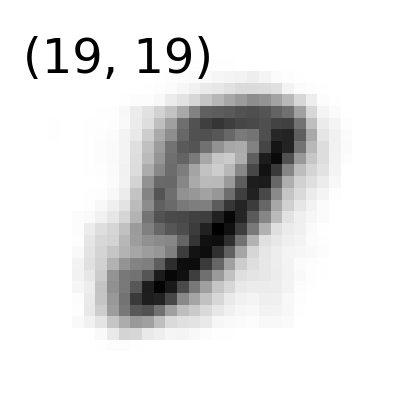

```mathematica
j=19;k=19;
im=Partition[m[[j*40+k]],28];
text=Inset[Style["("<>ToString[j]<>", "<>ToString[k]<>")",48],{7,26}];
pl=ArrayPlot[im,Epilog-> text]
```